# Data preprocessing: JLG data set NANOG, GATA6

## Supplementary material for Fischer et al "The salt-and-pepper pattern in mouse blastocysts is compatible with signalling beyond the nearest neighbours."

## Initialisation

```mathematica
baseDirectory=StringReplace[ParentDirectory[NotebookDirectory[]],"dataPreprocessing"->"analysisCode"];
```

```mathematica
<<(FileNameJoin[{baseDirectory,"CellNucleiSegmentation_v8.m"}]) (*code from Schmitz et al. Scientific Reports 2017*)
```

```mathematica
<<(FileNameJoin[{baseDirectory,"neighbourAnaFunctions_v2.m"}])(*code from Fischer et al. PLOS One 2020 and extensions*)
```

```mathematica
populationsColours={Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]};
```

## Separate embryos with less than 32 cells in extra stage category

#### Final Files (obtained from Silvia)

```mathematica
finalFNames=FileNames["*Final.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
data=Import/@finalFNames;
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
pos=Position[Length/@nucleiFeatures,z_/;z<32]
```

{{15},{120}}

```mathematica
(data=Import[finalFNames[[#[[1]]]]];Print[Length["NucleiFeatures"/.data]];dataNew=data/.Rule["CellNumberStage",_]->Rule["CellNumberStage",3.0];Print[("NucleiFeatures"/.data)==("NucleiFeatures"/.dataNew)];
Export[finalFNames[[#[[1]]]],dataNew])&/@pos
```

28

True

31

True

#### Final Data file

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
data=Import/@finalFNames;
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
pos=Position[Length/@nucleiFeatures,z_/;z<32];
```

```mathematica
(data=Import[finalFNames[[#[[1]]]]];Print[Length["NucleiFeatures"/.data]];newStage=("Staging"/.data)/.(3.5->3.0);dataNewStage=data/.Rule["Staging",_]->Rule["Staging",newStage];
dataNew=dataNewStage/.Rule["CellNumberStage",_]->Rule["CellNumberStage",3.0];
Print["Staging"/.dataNew];
Print["GlobalFeatures"/.dataNew];
Print[("NucleiFeatures"/.data)==("NucleiFeatures"/.dataNew)];
Export[finalFNames[[#[[1]]]],dataNew])&/@pos
```

28

{10 Young,10YNDsl2embr6.ome,3.}

{CellNumberStage→3.,ProximityCellGraph→-Graphics3D-,DelaunayCellGraph→-Graphics3D-,Surface→-Graphics3D-,SurfaceArea→8133.85,Volume→58580.,Centroid→{77.3337,83.7163,37.442},MinDistanceSurface→18.0307}

True

31

{4 Young,4YNDembryo1.ome,3.}

{CellNumberStage→3.,ProximityCellGraph→-Graphics3D-,DelaunayCellGraph→-Graphics3D-,Surface→-Graphics3D-,SurfaceArea→10086.4,Volume→77627.4,Centroid→{78.3423,74.6893,33.527},MinDistanceSurface→19.5648}

True

## Plot aligned data

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
Tally[staging[[All,-1]]]
```

{{4.,33},{3.5,96},{3.,2},{4.5,3}}

```mathematica
nucleiFeaturesICM=Table[Select[nucleiFeatures[[i]],("TE/ICM"/.#)≠"TE"&],{i,1,Length[nucleiFeatures]}];
```

```mathematica
exprICM={"Nanog-AvgShifted","Gata6-AvgShifted"}/.nucleiFeaturesICM;
```

```mathematica
exprICMByStage=Table[Select[Transpose[{staging,exprICM}],#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length/@exprICMByStage
```

{96,33,3}

```mathematica
Length[Flatten[#[[All,2]],1]]&/@exprICMByStage
```

{1968,769,74}

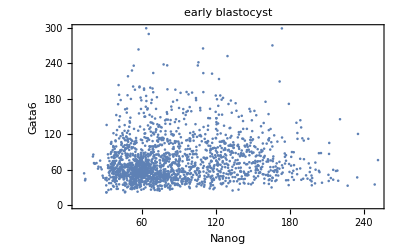
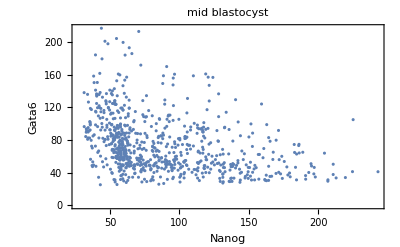
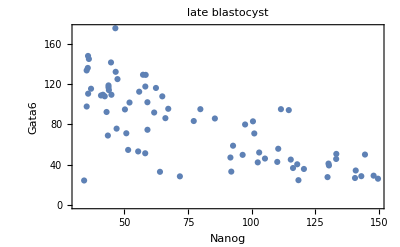
{-Graphics-,-Graphics-,-Graphics-}ICM cells

```mathematica
Labeled[Table[Show[ListPlot[#[[1;;2]]&/@Flatten[exprICMByStage[[i,All,2]],1],PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Nanog","Gata6"}],ImageSize->400,PlotLabel->({"early","mid","late"}[[i]]<>" blastocyst")],{i,1,3}],"ICM cells", Top]
```

## Plot populations

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
popValues={"TE/ICM","Quadrant"}/.nucleiFeatures;
```

```mathematica
popValuesICM=Table[Select[popValues[[i]],#[[1]]≠"TE"&],{i,1,Length[popValues]}];
```

```mathematica
populationsICM=Transpose[{staging,popValuesICM}];
```

```mathematica
popCountICM=Table[{populationsICM[[i,1]],{#,Count[populationsICM[[i,2,All,2]],#]}&/@{"N+G6+","N-G6-","N+G6-","N-G6+"}},{i,1, Length[populationsICM]}];
```

```mathematica
popCountICMByStage=Table[Select[popCountICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
populationsByStageICM=Table[Select[populationsICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
popCountByStageICM=Table[{#,Count[Flatten[populationsByStageICM[[i,All,2]],1][[All,2]],#]}&/@{"N-G6-","N+G6+","N+G6-","N-G6+"},{i,1,3}]
```

{{{N-G6-,305},{N+G6+,793},{N+G6-,408},{N-G6+,462}},{{N-G6-,56},{N+G6+,217},{N+G6-,232},{N-G6+,264}},{{N-G6-,5},{N+G6+,12},{N+G6-,25},{N-G6+,32}}}

```mathematica
popCountByStageICMTotal=Table[{#,Count[Flatten[populationsByStageICM[[i]][[All,2]]],#]}&/@{"N-G6-","N+G6+","N+G6-","N-G6+"},{i,1,3}]
```

{{{N-G6-,305},{N+G6+,793},{N+G6-,408},{N-G6+,462}},{{N-G6-,56},{N+G6+,217},{N+G6-,232},{N-G6+,264}},{{N-G6-,5},{N+G6+,12},{N+G6-,25},{N-G6+,32}}}

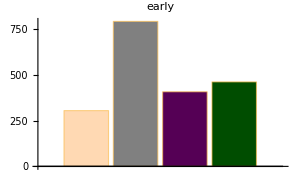
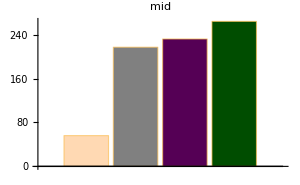
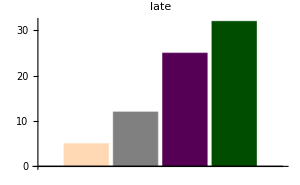

```mathematica
Labeled[Row[Table[BarChart[popCountByStageICMTotal[[i,All,2]],ImageSize->300,PlotLabel->Style[#,20,Black]&@({"early","mid","late"}[[i]]),ChartStyle->populationsColours,AxesStyle->Directive[Black,20]],{i,1,3}],"   "],SwatchLegend[populationsColours,{"DN","DP","Epi","PrE"}],Right]
```

#### Export absolute number of cells for each population to generate bar plot

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\populationCountByStage.xlsx"}],{"early"->Join[{{"Count for different populations", "","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corected and aligned","each row represents one embryo"},{"N+G6+","N-G6-","N+G6-","N-G6+"}},#[[-1,All,2]]&/@popCountICMByStage[[1]]],
"mid"->Join[{{"Count for different populations", "","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corected and aligned","each row represents one embryo"},{"N+G6+","N-G6-","N+G6-","N-G6+"}},#[[-1,All,2]]&/@popCountICMByStage[[2]]],
"late"->Join[{{"Count for different populations", "","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corected and aligned","each row represents one embryo"},{"N+G6+","N-G6-","N+G6-","N-G6+"}},#[[-1,All,2]]&/@popCountICMByStage[[3]]]}]
```

## ICM cells positive and negative

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
popValues={"TE/ICM","Quadrant"}/.nucleiFeatures;
```

```mathematica
popValuesICM=Table[Select[popValues[[i]],#[[1]]≠"TE"&],{i,1,Length[popValues]}];
```

```mathematica
populationsICM=Transpose[{staging,popValuesICM}];
```

```mathematica
populationsICMByStage=Table[Select[populationsICM,#[[1,-1]]==i&],{i,{3.5,4.0,4.5}}];
```

#### Nanog

```mathematica
nanogPositiveByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"N+"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{22,27,24,20,16,19,17,23,26,24,15,20,19,9,6,17,3,18,0,9,11,1,9,4,1,17,6,8,18,20,17,9,18,14,4,9,14,16,15,6,18,26,8,11,20,15,19,23,15,15,24,9,21,15,12,13,17,12,22,16,11,10,21,19,26,16,9,19,14,23,0,5,0,1,0,0,5,13,15,13,13,7,4,0,7,5,2,1,4,4,2,2,9,6,21,12},{15,22,20,20,9,6,7,11,15,10,24,20,16,11,27,10,15,29,14,14,16,15,13,6,19,14,2,6,1,12,3,13,14},{10,10,17}}

```mathematica
nanogNegativeByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"N-"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{1,0,1,4,0,1,3,0,1,1,1,7,5,14,16,5,10,9,15,16,11,24,7,22,16,7,22,13,6,4,9,5,7,3,15,12,6,7,8,4,7,3,3,8,7,3,3,2,3,3,3,3,1,2,3,8,2,3,2,0,0,5,5,2,3,4,17,3,1,1,24,14,17,16,22,19,6,8,3,7,3,18,25,19,16,20,9,21,11,7,11,12,8,10,4,9},{9,3,8,7,9,21,9,9,11,14,3,5,5,12,1,15,8,3,11,7,6,14,4,19,2,12,16,10,21,12,21,9,4},{16,11,10}}

```mathematica
Length/@nanogPositiveByStage
```

{96,33,3}

```mathematica
Length/@nanogNegativeByStage
```

{96,33,3}

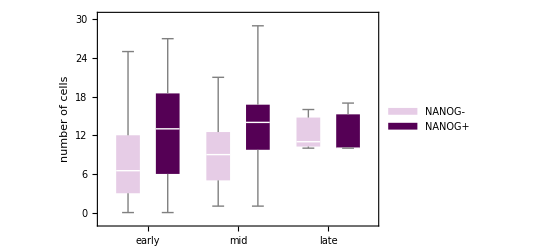

```mathematica
BoxWhiskerChart[Transpose[{nanogNegativeByStage,nanogPositiveByStage}],ChartLabels->{{"early","mid","late"},None},FrameLabel-> {None,"number of cells"},FrameStyle->Directive[Black,20],ChartLegends->(Style[#,Black,20]&/@{"NANOG-","NANOG+"}),ChartStyle->{Lighter[Purple,0.8],Darker[Purple]}]
```

#### Gata6

```mathematica
gata6PositiveByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"G6+"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{15,12,24,21,13,12,19,17,23,20,9,15,14,10,13,13,8,15,6,12,11,9,3,13,6,22,5,11,2,14,11,6,3,2,3,0,7,11,14,7,15,29,11,17,20,15,22,24,18,15,27,12,21,16,13,14,18,14,23,12,10,10,23,21,27,18,16,13,14,17,22,16,7,9,14,17,8,15,8,2,10,4,11,9,14,20,3,10,6,5,10,3,11,12,18,15},{11,19,14,16,9,16,12,16,16,8,12,20,9,14,25,15,14,32,15,12,11,17,6,25,7,14,13,8,15,16,17,15,12},{18,10,16}}

```mathematica
gata6NegativeByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"G6-"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{8,15,1,3,3,8,1,6,4,5,7,12,10,13,9,9,5,12,9,13,11,16,13,13,11,2,23,10,22,10,15,8,22,15,16,21,13,12,9,3,10,0,0,2,7,3,0,1,0,3,0,0,1,1,2,7,1,1,1,4,1,5,3,0,2,2,10,9,1,7,2,3,10,8,8,2,3,6,10,18,6,21,18,10,9,5,8,12,9,6,3,11,6,4,7,6},{13,6,14,11,9,11,4,4,10,16,15,5,12,9,3,10,9,0,10,9,11,12,11,0,14,12,5,8,7,8,7,7,6},{8,11,11}}

```mathematica
Length/@gata6PositiveByStage
```

{96,33,3}

```mathematica
Length/@gata6NegativeByStage
```

{96,33,3}

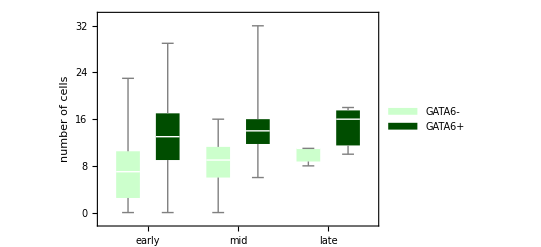

```mathematica
BoxWhiskerChart[Transpose[{gata6NegativeByStage,gata6PositiveByStage}],ChartLabels->{{"early","mid","late"},None},FrameLabel-> {None,"number of cells"},FrameStyle->Directive[Black,20],ChartLegends->(Style[#,Black,20]&/@{"GATA6-","GATA6+"}),ChartStyle->{Lighter[Green,0.8],Darker[Green,0.7]}]
```

#### Export

```mathematica
allCells=Transpose[{nanogNegativeByStage[[#]],nanogPositiveByStage[[#]],gata6NegativeByStage[[#]],gata6PositiveByStage[[#]]}]&/@{1,2,3};
```

```mathematica
exportList=Table[{"early","mid","late"}[[i]]->Join[{{"Our embryo data: number of positive and negative cells", "","","",DateString[]},{"ICM cells, Staging by cell number","each row represents one embryo"},{"N-","N+","G6-","G6+"}},allCells[[i]]],{i,1,3}];
```

```mathematica
(Length[#]-3)&/@exportList[[All,2]]
```

{96,33,3}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results","positiveNegativeCells.xlsx"}],exportList]
```

## Calculate and export neighbour comparison files

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
data=Import[#]&/@finalFNames;
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
staging=("Staging"/.data);
```

```mathematica
dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.#))&/@data}];
```

```mathematica
gata6Gata6Comp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Gata6-AvgShifted","Gata6-AvgShifted"];
```

```mathematica
nanogNanogComp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Nanog-AvgShifted","Nanog-AvgShifted"];
```

```mathematica
gata6NanogComp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Gata6-AvgShifted","Nanog-AvgShifted"];
```

```mathematica
nanogGata6Comp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Nanog-AvgShifted","Gata6-AvgShifted"];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\nanogNanogComp.mx"}],nanogNanogComp]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\gata6Gata6Comp.mx"}],gata6Gata6Comp]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\gata6NanogComp.mx"}],gata6NanogComp]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\nanogGata6Comp.mx"}],nanogGata6Comp]
```